```mathematica
f[x_]:=-(x-0.004214)+√((x-0.004214)^2+0.0216x)
```

```mathematica
g[x_]:=(f[x]^2+4x*f[x]+0.0024f[x]+4x^2+0.0048x+4x)^2-8f[x]^3-48x*f[x]^2-96x^2*f[x]-0.0384x*f[x]-64x^3-0.0768x^2
```

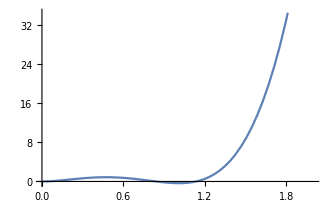

```mathematica
Plot[g[x],{x,0,2}]
```

```mathematica
g[x]
```

-8 (0.004214+√((-0.004214+x)^2+0.0216 x)-x)^3-0.0384 (0.004214+√((-0.004214+x)^2+0.0216 x)-x) x-48 (0.004214+√((-0.004214+x)^2+0.0216 x)-x)^2 x-0.0768 x^2-96 (0.004214+√((-0.004214+x)^2+0.0216 x)-x) x^2-64 x^3+(0.0024 (0.004214+√((-0.004214+x)^2+0.0216 x)-x)+(0.004214+√((-0.004214+x)^2+0.0216 x)-x)^2+4.0048 x+4 (0.004214+√((-0.004214+x)^2+0.0216 x)-x) x+4 x^2)^2

```mathematica
Solve[-8 (0.004214+√((-0.004214+x)^2+0.0216 x)-x)^3-0.0384 (0.004214+√((-0.004214+x)^2+0.0216 x)-x) x-48 (0.004214+√((-0.004214+x)^2+0.0216 x)-x)^2 x-0.0768 x^2-96 (0.004214+√((-0.004214+x)^2+0.0216 x)-x) x^2-64 x^3+(0.0024 (0.004214+√((-0.004214+x)^2+0.0216 x)-x)+(0.004214+√((-0.004214+x)^2+0.0216 x)-x)^2+4.0048 x+4 (0.004214+√((-0.004214+x)^2+0.0216 x)-x) x+4 x^2)^2==0,x]
```

{{x→-0.000444783},{x→0.000704619},{x→0.840164},{x→1.13557}}